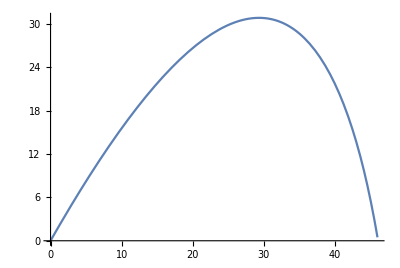

```mathematica
(* Исходные параметры *)
v = 28.4;
angle = Pi/3;
g = 9.8;
ResistForce = 4;
Mass = 2;

(* Получение численного решения систем дифференциальных уравнений *)
ndsY = NDSolve[
{y''[t] == -g,  y'[0] == v * Sin[angle],  y[0] == 0},
 y, 
{t, 0, 10}
];

ndsX = NDSolve[
{ x''[t] == -ResistForce / Mass,  x'[0] == v*Cos[angle], x[0] == 0}, 
x, 
{t, 0, 10}];

(* Построение графика *)
ParametricPlot[
{Evaluate[{x[t],y[t]}/.Flatten@{ndsX, ndsY}]}, 
{t, 0, 5}
]
```